```mathematica
Manipulate[
Module[{arrows,ptv,bn,k,kT,Cp,Qg,Qr,x,Tmax,UA,V,ΔH,sol,solm,pp1,pp2,p1,p2,p3},
arrows=Line[x_]:>Sequence[Arrowheads[Table[.04,{7}]],Arrow@Line[x]];
ptv=Sequence[AspectRatio->1/GoldenRatio,Frame->True,Axes->False,LabelStyle->Black,PlotStyle->Blue,ImageSize->{450,320},ImagePadding->{{80,5},{50,5}}];
bn=Sequence[LabelStyle->Black,ImageSize->{450,320},Axes->False,ImagePadding->{{50,5},{50,10}},Frame->True];

k=0.004*Exp[-1.5*10^4*(1/T[t]-1/298)];
kT[Temp_]=0.004*Exp[-1.5*10^4*(1/Temp-1/298)];
Cp=4*10^3;UA=3400;V=10;ΔH=-2.2*10^5;
Qg=-kT[Temp]/(1+kT[Temp]*τ)*ΔH*2;
Qr=Cp/τ*(Temp-298)+UA/V*(Temp-300);
x=1-Ca[t]/2;
(*Tmax=Quiet@If[sws==5,Evaluate[Temp/.Solve[Qr==Qg,Temp][[1]]]];*)
Tmax=Quiet@If[sws==5,Evaluate[Temp/.FindRoot[Qr==Qg,{Temp,100}]]];
sol=Flatten@NDSolve[{
Ca'[t]==(2-Ca[t])/τ-k*Ca[t],
T'[t]==UA/(V*Cp)*(300-T[t])+(298-T[t])/τ-ΔH/Cp*k*Ca[t],
Ca[0]==Cao,
T[0]==To},
{Ca[t],T[t]},
{t,0,200}];
solm=Flatten@NDSolve[{
Ca'[t]==(2-Ca[t])/τ-k*Ca[t],
T'[t]==UA/(V*Cp)*(300-T[t])+(298-T[t])/τ-ΔH/Cp*k*Ca[t],
Ca[0]==#,
T[0]==To},
{Ca[t],T[t]},
{t,0,200}]&/@Table[j,{j,0,2,0.25}];

pp1=ParametricPlot[{T[t],Ca[t]}/.solm,{t,0,200},Evaluate@ptv,PlotRange->All,FrameLabel->{Style["temperature (K)",16],Style["concentration (kmol/m^3)",16]}]/.arrows;
pp2=ParametricPlot[{T[t],x}/.sol,{t,0,200},Evaluate@ptv,PlotRange->{All,{0,1.1}},FrameLabel->{Style["temperature (K)",16],Style["conversion",16]}]/.arrows;
p1=Plot[x/.sol,{t,0,200},Evaluate@bn,PlotRange->{0,1.1},PlotStyle->{Thick,Black},FrameLabel->{Style["time (min)",16],Style["conversion",16]}];
p2=Plot[T[t]/.sol,{t,0,200},Evaluate@bn,PlotRange->All,PlotStyle->{Thick,Orange},FrameLabel->{Style["time (min)",16],Style["temperature (K)",16]}];
p3=Plot[{Qr*10^-3,Qg*10^-3},{Temp,289,425},Evaluate@bn,PlotRange->All,PlotStyle->{{Thick,Blue},{Thick,Red}},FrameLabel->{Style["temperature (K)",16],Style["energy rate per volume (MJ/m^3/min)",16]},PlotLabel->Style[Row[{"upper steady-state temperature"," = ",NumberForm[Tmax,{3,0}]," K"}],16],
Epilog->Inset[Graphics[Text@Grid[{
{Style["—",20,Blue],Style["heat removed",15]},
{Style["—",20,Red],Style["heat generated",15]}
},Alignment->"heat"]],Scaled[{0.25,0.85}]
]];

Switch[sws,1,Show[pp1],2,Show[pp2],3,Show[p1],4,Show[p2],5,Show[p3]]
],(*Column[{
Row[{"phase plane:",Control[{{sws,1,""},{1->"several initial concentrations",2->"one initial concentration"},SetterBar,Appearance->"Row"}]}],
Control[{{sws,1,""},{3->"conversion v time",4->"temperature v time",5->"energy v temperature"},SetterBar,Appearance->"Row"}]
},Alignment->Center],*)
(*Control[{{sws,1,"phase plane:"},{1->"several initial concentrations",2->"one initial concentration"},SetterBar,Appearance->"Row"}],
Control[{{sws,1,""},{3->"conversion v time",4->"temperature v time",5->"energy v temperature"},SetterBar,Appearance->"Row"}],*)
Grid[{
{"phase plane:",Control[{{sws,1,""},{1->"several initial concentrations",2->"one initial concentration"},SetterBar,Appearance->"Row"}]},
{"",Control[{{sws,1,""},{3->"conversion v time",4->"temperature v time",5->"energy v temperature"},SetterBar,Appearance->"Row"}]}
},Alignment->Left],
PaneSelector[{
1->Control[{{To,315,"initial reactor temperature (K)"},200,450,1,Appearance->"Labeled"}],
2->Column[{
Control[{{To,315,"initial reactor temperature (K)"},200,450,1,Appearance->"Labeled"}],
Control[{{Cao,2,"initial reactor concentration (kmol/m^3)"},0,2,0.1,Appearance->"Labeled"}]
}],
3->Column[{
Control[{{To,315,"initial reactor temperature (K)"},200,450,1,Appearance->"Labeled"}],
Control[{{Cao,2,"initial reactor concentration (kmol/m^3)"},0,2,0.1,Appearance->"Labeled"}]
}],
4->Column[{
Control[{{To,315,"initial reactor temperature (K)"},200,450,1,Appearance->"Labeled"}],
Control[{{Cao,2,"initial reactor concentration (kmol/m^3)"},0,2,0.1,Appearance->"Labeled"}]
}],
5->Control[{{τ,38.5,"residence time (min)"},1,50,0.5,Appearance->"Labeled"}]
},Dynamic@sws]
]
```

```mathematica
(*Caf=2;Tf=298;tf=200;
k=km*Exp[-Ea*(T[t]^-1-Tm^-1)];
km=0.004;Ea=1.5*10^4;Tm=298;
Cp=4*10^3;UA=3400;V=10;Ta=300;ΔH=-2.2*10^5;
τ=38.5
sol=NDSolve[{
Ca'[t]==(Caf-Ca[t])/τ-k*Ca[t],
T'[t]==UA/(V*Cp)*(Ta-T[t])+(Tf-T[t])/τ-ΔH/Cp*k*Ca[t],
Ca[0]==X,
T[0]==To},
{Ca[t],T[t]},
{t,0,tf}]*)
```

```mathematica
(*ParametricPlot3D[{{Sin[u],Cos[u],u/10},{Cos[u],Sin[u],u/10}},{u,0,20}]/.Line[x_]:>Sequence[Arrowheads[Table[.025,{50}]],Arrow@Line[x]]*)
```

```mathematica
(*Line[x_]:>Sequence[Arrowheads[Table[.025,{10}]],Arrow@Line[x]]*)
```

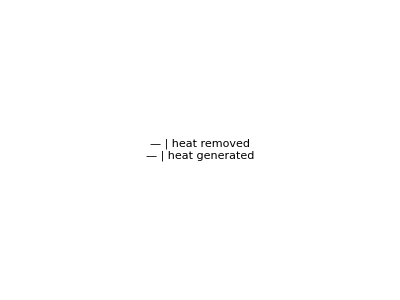

```mathematica
Graphics[Text@Grid[{
{Style["—",20,Blue],Style["heat removed",15]},
{Style["—",20,Red],Style["heat generated",15]}
},Alignment->"heat"]]
```